```mathematica
(*Sección 16*)
(*19*)
```

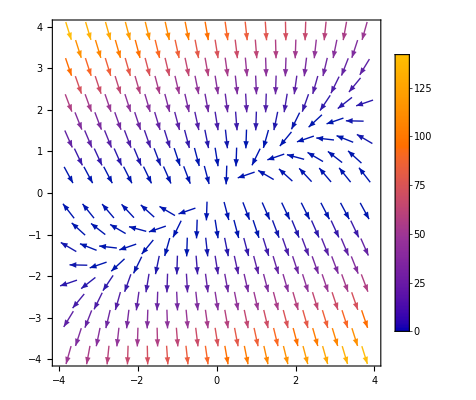

```mathematica
VectorPlot[{y^2-2x y,3x y-6y^2 },{x,-4,4},{y,-4,4},PlotLegends->Automatic]
```

```mathematica
(*Los puntos que hacen F = 0 son aquellos en que x=y y, y=y=0*)
```

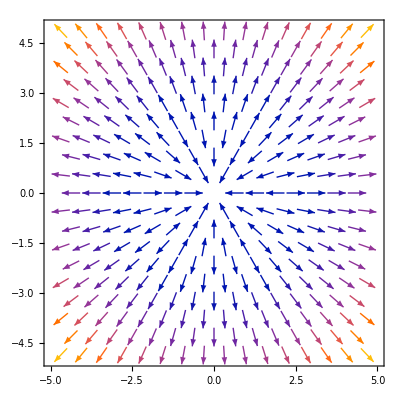

```mathematica
(*20*)
VectorPlot[{x*(x^2+y^2-2*(Sqrt[x^2+y^2])),y*(x^2+y^2-2*(Sqrt[x^2+y^2]))},{x,-5,5},{y,-5,5}]
```

```mathematica
(*Se hace cero cuando "x" es cero y "y" es cero*)
```

```mathematica
A1=ContourPlot[Log[1+x^2+2 y^2],{x,-4,4},{y,-4,4},AxesLabel->Automatic];
```

```mathematica
A2=VectorPlot[{2x/(1+x^2+2y^2),4y/(1+x^2+2y^2)},{x,-4,4},{y,-4,4}];
```

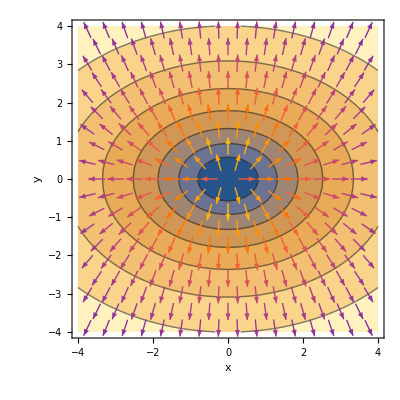

```mathematica
Show[A1,A2]
```

```mathematica
(*El campo se expande con la altura de la región deseada*)
```

```mathematica
A3=ContourPlot[Cos[x]-2Sin[y],{x,0,2Pi},{y,0,2Pi},AxesLabel->Automatic];
```

```mathematica
A4=VectorPlot[{-Sin[x],-2Cos[x]},{x,0,2Pi},{y,0,2Pi}];
```

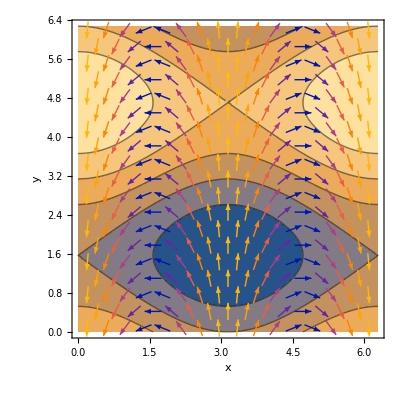

```mathematica
Show[A3,A4]
```

```mathematica
(*El campo vectorial cambia con la altura del mapa de contorno*)
```